```mathematica
ω:=4
μ:=0.5
```

```mathematica
ω
```

1

```mathematica
w[z_]:=z^2+ω −ω*μ*(Hypergeometric1F1[1/4,1/2,z^2/(4*1)]−z*2/(Sqrt[2*1]) *2 Gamma[3/4]/(Gamma[1/4]) * Hypergeometric1F1[3/4,3/2,z^2/(4*1)]);
w[z]
sol=NSolve[w[z]==0 && Abs[z]<20,z]
```

4+z^2-2. (-1/8 ⅇ^(z^2/8) (z^2)^(1/4) BesselI[-1/4,z^2/8] Gamma[-1/4]-(4 √2 ⅇ^(z^2/8) z BesselI[1/4,z^2/8] Gamma[3/4] Gamma[5/4])/((z^2)^(1/4) Gamma[1/4]))

{{z→-14.2881-13.4556 ⅈ},{z→-14.2881+13.4556 ⅈ},{z→-13.8354-12.9869 ⅈ},{z→-13.8354+12.9869 ⅈ},{z→-13.3669-12.5012 ⅈ},{z→-13.3669+12.5012 ⅈ},{z→-12.8809-11.9964 ⅈ},{z→-12.8809+11.9964 ⅈ},{z→-12.3751-11.4701 ⅈ},{z→-12.3751+11.4701 ⅈ},{z→-11.8469-10.9193 ⅈ},{z→-11.8469+10.9193 ⅈ},{z→-11.293-10.3404 ⅈ},{z→-11.293+10.3404 ⅈ},{z→-10.7092-9.72862 ⅈ},{z→-10.7092+9.72862 ⅈ},{z→-10.0897-9.07761 ⅈ},{z→-10.0897+9.07761 ⅈ},{z→-9.42701-8.37885 ⅈ},{z→-9.42701+8.37885 ⅈ},{z→-8.71021-7.62017 ⅈ},{z→-8.71021+7.62017 ⅈ},{z→-7.92266-6.78315 ⅈ},{z→-7.92266+6.78315 ⅈ},{z→-5.9973-4.72594 ⅈ},{z→-5.9973+4.72594 ⅈ},{z→-5.9973-4.72594 ⅈ},{z→-4.65949+3.30913 ⅈ},{z→-4.65949-3.30913 ⅈ},{z→-1.34579+0. ⅈ},{z→-0.925839-1.7718 ⅈ},{z→-0.925839+1.7718 ⅈ},{z→4.05521-2.13436 ⅈ},{z→4.05521+2.13436 ⅈ},{z→5.57005-3.92355 ⅈ},{z→5.57005+3.92355 ⅈ},{z→6.68182-5.18807 ⅈ},{z→6.68182+5.18807 ⅈ},{z→8.429-7.12073 ⅈ},{z→8.429+7.12073 ⅈ},{z→9.1683-7.92384 ⅈ},{z→9.1683+7.92384 ⅈ},{z→9.84868-8.657 ⅈ},{z→9.84868+8.657 ⅈ},{z→10.4826-9.33567 ⅈ},{z→10.4826+9.33567 ⅈ},{z→11.0785-9.97034 ⅈ},{z→11.0785+9.97034 ⅈ},{z→11.6427-10.5685 ⅈ},{z→11.6427+10.5685 ⅈ},{z→12.1798-11.1358 ⅈ},{z→12.1798+11.1358 ⅈ},{z→12.6934-11.6766 ⅈ},{z→12.6934+11.6766 ⅈ},{z→13.1863-12.1941 ⅈ},{z→13.1863+12.1941 ⅈ},{z→13.661-12.6912 ⅈ},{z→13.661+12.6912 ⅈ},{z→14.1193-13.17 ⅈ},{z→14.1193+13.17 ⅈ},{z→14.5628-13.6325 ⅈ},{z→14.5628+13.6325 ⅈ}}

```mathematica
sol
```

{}

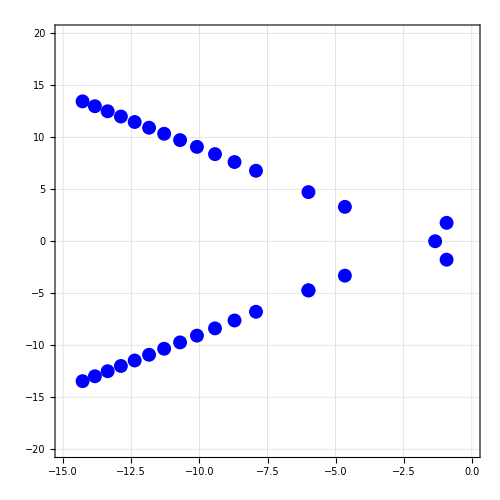

```mathematica
Plot[{Re[w/.z->I*y]==0},{y,−20,0},RegionFunction ->(Abs[I #2]<70&),Epilog->{Blue,PointSize[0.02],Point[{Re[z],Im[z]}]/.sol},PlotStyle->None,Frame->True,FrameStyle->Directive[Black,Thick],GridLines->Automatic,GridLinesStyle->Directive[Black,Thick],Axes->True,PlotRange->{{−15,0},{−20,20}},ImageSize->500,AspectRatio->1,BaseStyle->FontSize->20]
```